### Random vs. evolved rules

#### Random

```mathematica
Table[ArrayPlot[CellularAutomaton[{ResourceFunction["RandomCA"][{2, 2}]["RuleNumber"], 2, 2}, RandomInteger[1,500], 300]], 20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[CellularAutomaton[{ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"], 3, 1
}, RandomInteger[1,500], 300]], 20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

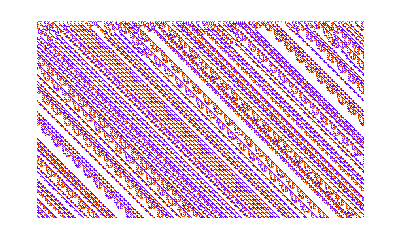
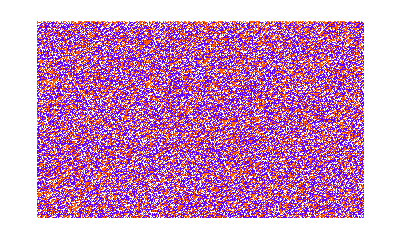
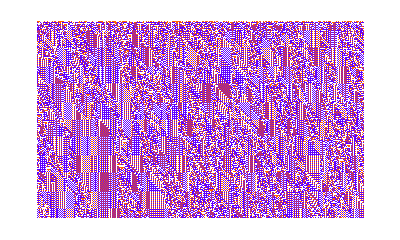
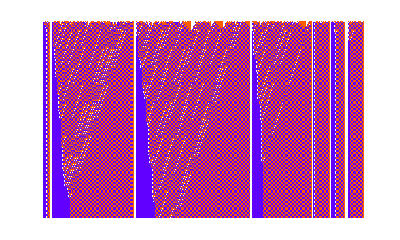
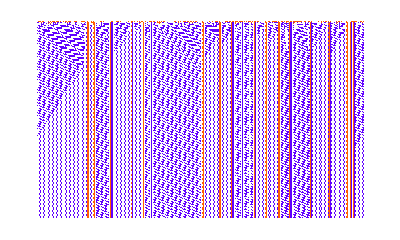
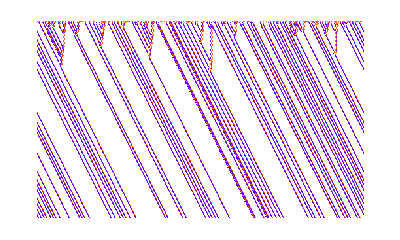
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ru},
rus =  NestWhile[
Function[rus, ru  = ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"];If[Last[IntegerDigits[ru, 3, 3^3]]== 0, Append[rus, ru], rus]],
 {}, Length[#] < 20&];
ArrayPlot[CellularAutomaton[{ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"], 3, 1
}, RandomInteger[1,500], 300],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ rus
]
```

```mathematica
Module[{rus = {}, ru}, While[Length[rus] <20, ru =ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"]; If[ru == AppendTo[rus, ru] ]
```

#### Enforcing last digit in rule to be == 0

#### Evolved high-fitness

```mathematica
SeedRandom[233332];RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&], All]
```

<|{1346060446827,134217727}→107,{829107378909,134217727}→107,{3355471467168,134217727}→94,{3028929311652,134217727}→102,{3597345782925,134217727}→100,{2205091360590,134217727}→105,{5490928491741,134217727}→105,{1556791350930,134217727}→106,{5392983480306,134217727}→99,{3183459840357,134217727}→98,{5277933939093,134217727}→100,{3030048172077,134217727}→110,{5453442454407,134217727}→97,{3109525018056,134217727}→97,{5492911159977,134217727}→97,{2663964499281,134217727}→102,{2853395704023,134217727}→93,{2602394636856,134217727}→94,{2564050580565,134217727}→104,{2056354546506,134217727}→91,{755876403351,134217727}→94,{1186862096697,134217727}→96,{5426632498200,134217727}→106,{6096315644916,134217727}→107,{5943951685527,134217727}→105,{1815729217701,134217727}→106,{1795195359009,134217727}→95,{2346891931455,134217727}→96,{715200619581,134217727}→95,{1186905143418,125829119}→96,{604439967615,134217727}→97,{5520791615883,134217727}→107,{6895974089229,134217727}→92,{1680083714313,134217727}→96,{5444159008794,134217727}→103,{445188530436,134217727}→108,{6002459520102,134217727}→91,{3554363782194,134217727}→90,{1434463122498,134217727}→109,{6336881038824,134217727}→109,{552157329372,134217727}→94,{1159321843575,134217727}→105,{2152820534388,134217727}→93,{338237267406,134152191}→91,{5487111842127,134217727}→95,{1495284082011,134217727}→91,{5180604732054,134217727}→94,{2200542109638,134217727}→95,{5451433748883,134217727}→106,{2571010270503,134217727}→93,{2882514066405,134217727}→107,{6899460931977,134217727}→94,{5624611709517,134217727}→90,{3167656930710,134217727}→93,{4777263497679,134217727}→107,{5182527818769,134217727}→96,{1501782582840,134217727}→90,{3418412612775,134217727}→106,{5967246160761,134217727}→94,{6573130800876,134217727}→98,{6317440535169,134217727}→110,{1995908801406,134217727}→110,{3017349566286,134217727}→95,{5625429164079,134217727}→110,{1901790124836,134217727}→99,{2733742170735,134217727}→96,{3550920103563,134217727}→95,{3031210551669,134217727}→94,{4609814469621,134217727}→95,{3038270332227,134217727}→110,{509093422764,134217727}→95,{3300926665326,134217727}→106,{6847265928957,134217727}→105,{3329128074258,134217727}→90,{2564052174888,134217727}→104,{7171470924378,134217727}→93,{5631282868758,134217727}→103,{2501939449494,134217727}→90,{3032456013177,134217727}→101,{1341839999664,134217727}→90,{1582452097713,134217727}→108,{3868211112621,134217727}→91,{3146305795944,134217727}→99,{1473897816006,134217727}→91,{2205120174315,134217727}→91,{4112320982073,134217727}→99,{4359919332795,134217727}→105,{1153525057920,134217727}→101,{407196835083,134217727}→105,{6018359568972,134217727}→97,{5339454376749,134217727}→100,{5162790870204,134217727}→104,{3184695025989,134217727}→109,{4264696737519,134217727}→94,{236403443817,134217727}→100|>

```mathematica
Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]
```

<|{1341839999664,134217727}→90,{1501782582840,134217727}→90,{2501939449494,134217727}→90,{3329128074258,134217727}→90,{3554363782194,134217727}→90,{5624611709517,134217727}→90,{1473897816006,134217727}→91,{1495284082011,134217727}→91,{2056354546506,134217727}→91,{2205120174315,134217727}→91,{338237267406,134152191}→91,{3868211112621,134217727}→91,{6002459520102,134217727}→91,{6895974089229,134217727}→92,{2152820534388,134217727}→93,{2571010270503,134217727}→93,{2853395704023,134217727}→93,{3167656930710,134217727}→93,{7171470924378,134217727}→93,{2602394636856,134217727}→94,{3031210551669,134217727}→94,{3355471467168,134217727}→94,{4264696737519,134217727}→94,{5180604732054,134217727}→94,{552157329372,134217727}→94,{5967246160761,134217727}→94,{6899460931977,134217727}→94,{755876403351,134217727}→94,{1795195359009,134217727}→95,{2200542109638,134217727}→95,{3017349566286,134217727}→95,{3550920103563,134217727}→95,{4609814469621,134217727}→95,{509093422764,134217727}→95,{5487111842127,134217727}→95,{715200619581,134217727}→95,{1186862096697,134217727}→96,{1186905143418,125829119}→96,{1680083714313,134217727}→96,{2346891931455,134217727}→96,{2733742170735,134217727}→96,{5182527818769,134217727}→96,{3109525018056,134217727}→97,{5453442454407,134217727}→97,{5492911159977,134217727}→97,{6018359568972,134217727}→97,{604439967615,134217727}→97,{3183459840357,134217727}→98,{6573130800876,134217727}→98,{1901790124836,134217727}→99,{3146305795944,134217727}→99,{4112320982073,134217727}→99,{5392983480306,134217727}→99,{236403443817,134217727}→100,{3597345782925,134217727}→100,{5277933939093,134217727}→100,{5339454376749,134217727}→100,{1153525057920,134217727}→101,{3032456013177,134217727}→101,{2663964499281,134217727}→102,{3028929311652,134217727}→102,{5444159008794,134217727}→103,{5631282868758,134217727}→103,{2564050580565,134217727}→104,{2564052174888,134217727}→104,{5162790870204,134217727}→104,{1159321843575,134217727}→105,{2205091360590,134217727}→105,{407196835083,134217727}→105,{4359919332795,134217727}→105,{5490928491741,134217727}→105,{5943951685527,134217727}→105,{6847265928957,134217727}→105,{1556791350930,134217727}→106,{1815729217701,134217727}→106,{3300926665326,134217727}→106,{3418412612775,134217727}→106,{5426632498200,134217727}→106,{5451433748883,134217727}→106,{1346060446827,134217727}→107,{2882514066405,134217727}→107,{4777263497679,134217727}→107,{5520791615883,134217727}→107,{6096315644916,134217727}→107,{829107378909,134217727}→107,{1582452097713,134217727}→108,{445188530436,134217727}→108,{1434463122498,134217727}→109,{3184695025989,134217727}→109,{6336881038824,134217727}→109,{1995908801406,134217727}→110,{3030048172077,134217727}→110,{3038270332227,134217727}→110,{5625429164079,134217727}→110,{6317440535169,134217727}→110|>

```mathematica
KeyValueMap[ArrayPlot[CellularAutomaton[{First[#1], 3, 1}, RandomInteger[1,500], 300], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### From seed

```mathematica
SeedRandom[444444];
Module[{ru},
rus =  NestWhile[
Function[rus, ru  = ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"];If[Last[IntegerDigits[ru, 3, 3^3]]== 0, Append[rus, ru], rus]],
 {}, Length[#] < 20&];
ArrayPlot[CellularAutomaton[{#, 3, 1}, {{1}, 0}, {200, All}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ rus
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
KeyValueMap[ArrayPlot[CellularAutomaton[{First[#1], 3, 1}, {{1}, 0}, {200, All}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
KeyValueMap[ArrayPlot[CellularAutomaton[{First[#1], 3, 1}, {{1}, 0}, {200, {-50, 50}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Smaller random

```mathematica
KeyValueMap[ArrayPlot[CellularAutomaton[{First[#1], 3, 1}, {RandomChoice[{1, 2}, 5], 0}, {200, All}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Comparing pieces of “biological matter” with random matter

#### Attempt 1

```mathematica
{{"[◼]", "nonzeroRange"}}[{0, 0, 1, 1, 1, 1, 0}]
```

{3,6}

```mathematica
ResourceFunction["ArrayCrop"][{{0,0, 1}, {0, 1, 1}}]
```

{{0,1},{1,1}}

```mathematica
KeyValueMap[{{"[◼]", "nonzeroRange"}}/@ResourceFunction["ArrayCrop"][ CellularAutomaton[{First[#1], 3, 1}, {{1}, 0}, {200, All}]]&,Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]]
```

First get the body

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},{{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {400, {-30, 40}}, #]&/@ {{"[◼]", "allperts"}}[CellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}]]];
```

```mathematica
widths=If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@#&/@pcas[[All,1]];
```

```mathematica
width0=If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {400, {-30, 40}}, <||>];
```

```mathematica
GraphicsRow[Show[ListStepPlot[Pick[widths,widths[[#,25]]<12&&widths[[#,25]]!=0&/@Range[Length[pcas]]],PlotRange->#,PlotStyle->RGBColor[0.95, 0.627, 0.1425],AspectRatio->.4,Frame->True,FrameLabel->{"time","width"}],ListStepPlot[width0,PlotStyle->RGBColor[0.24, 0.6, 0.8]]]&/@{{{0,50},{0,30}},{{0,240},Automatic}}]
```

#### Matching sillhoutte

Some candidates for comparison

```mathematica
SeedRandom[444445];
Module[{ru},
rus =  NestWhile[
Function[rus, ru  = ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"];If[Last[IntegerDigits[ru, 3, 3^3]]== 0, Append[rus, ru], rus]],
 {}, Length[#] < 20&];
ArrayPlot[CellularAutomaton[{#, 3, 1}, {{1}, 0}, {200, All}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ rus
][[{4, 6, 10, 12, 18, 20}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[444446];
Module[{ru},
rus =  NestWhile[
Function[rus, ru  = ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"];If[Last[IntegerDigits[ru, 3, 3^3]]== 0, Append[rus, ru], rus]],
 {}, Length[#] < 20&];
ArrayPlot[CellularAutomaton[{#, 3, 1}, {{1}, 0}, {{100, 250}, {-75, 25}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ rus[[{-3}]]
]
```

{-Graphics-}

```mathematica
SeedRandom[444444];
Module[{ru},
rus =  NestWhile[
Function[rus, ru  = ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"];If[Last[IntegerDigits[ru, 3, 3^3]]== 0, Append[rus, ru], rus]],
 {}, Length[#] < 20&];
ArrayPlot[CellularAutomaton[{#, 3, 1}, {{1}, 0}, {{50, 200}, {-50, 50}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ rus
][[3]]
```

-Graphics-

```mathematica
ranges = KeyValueMap[{{"[◼]", "nonzeroRange"}}/@ CellularAutomaton[{First[#1], 3, 1}, {{1}, 0}, {150, {-50, 50}}]&,Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]];
```

```mathematica
Transpose[{Module[{randmatter = CellularAutomaton[{rus[[-3]], 3, 1}, {{1}, 0}, {{100, 250}, {-75, 25}}]},ArrayPlot[#, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@
MapIndexed[
If[# == {}, Table[0, 100], 
ReplacePart[randmatter[[Last[#2]]],Thread[Join[Range[First[#1]], Range[Last[#1], Length[randmatter[[Last[#2]]]]]]->0]]]&,ranges, {2}]], 
KeyValueMap[ArrayPlot[CellularAutomaton[{First[#1], 3, 1}, {{1}, 0}, {150, {-50, 50}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]]}][[;;20]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Transpose[{Module[{randmatter = CellularAutomaton[{rus[[3]], 3, 1}, {{1}, 0}, {{50, 200}, {-50, 50}}]},ArrayPlot[#, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@
MapIndexed[
If[# == {}, Table[0, 100], 
ReplacePart[randmatter[[Last[#2]]],Thread[Join[Range[First[#1]], Range[Last[#1], Length[randmatter[[Last[#2]]]]]]->0]]]&,ranges, {2}]], 
KeyValueMap[ArrayPlot[CellularAutomaton[{First[#1], 3, 1}, {{1}, 0}, {150, {-50, 50}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]]}][[;;20]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

#### symmetric quiescent rules from random initial conditions evolved vs. random

```mathematica
Options[ResourceFunction["RandomCA"]]
```

{}

```mathematica
Table[SeedRandom[333322 + i];ArrayPlot[CellularAutomaton[{ResourceFunction["RandomCA"][{3, 1},"Type"->"Symmetric", "Quiescent"->True]["RuleNumber"], 3, 1
}, RandomInteger[1,500], 300], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], {i, 20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomSample[Values[Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]], 20]
```

{109,107,97,95,101,102,95,103,96,98,91,102,96,91,90,90,96,94,94,103}

```mathematica
SeedRandom[555444];
ArrayPlot[CellularAutomaton[{First[#], 3, 1}, RandomInteger[1,500], 300], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ RandomSample[Keys[Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]], 20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### symmetric quiescent rules from seed inital condition evolved vs. random

```mathematica
Table[SeedRandom[333322 + i];ArrayPlot[CellularAutomaton[{ResourceFunction["RandomCA"][{3, 1},"Type"->"Symmetric", "Quiescent"->True]["RuleNumber"], 3, 1
}, {{1}, 0}, {115, All}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], {i, 20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[555444];
ArrayPlot[CellularAutomaton[{First[#], 3, 1}, {{1}, 0}, {115, All}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ RandomSample[Keys[Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]], 20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Matching silhoutte with random symmetric quiescent rules

```mathematica
SeedRandom[444445];
ArrayPlot[CellularAutomaton[{#RuleNumber, 3, 1}, {{1}, 0}, {150, {-50, 50}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ Table[ResourceFunction["RandomCA"][{3, 1}, "Type"->"Symmetric","Quiescent"->True], 
30][[{4}]]
```

{-Graphics-}

```mathematica
SeedRandom[444445];
Table[ResourceFunction["RandomCA"][{3, 1}, "Type"->"Symmetric","Quiescent"->True], 
30][[4]]
```

<|RuleNumber→1006690012323,Colors→3|>

```mathematica
SeedRandom[3245];
mcode=ResourceFunction["RandomCA"][{3},"Type"->"Multiset","Quiescent"->{0,1,2}]
```

```mathematica
ArrayPlot[CellularAutomaton[{1006690012323, 3, 1}, {{1}, 0}, {{100, 250}, {-75, 25}}]]
```

```mathematica
Transpose[{Module[{randmatter = CellularAutomaton[{1006690012323, 3, 1}, {{1}, 0}, {150, {-50, 50}}]},ArrayPlot[#, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@
MapIndexed[
If[# == {}, Table[0, 100], 
ReplacePart[randmatter[[Last[#2]]],Thread[Join[Range[First[#1]], Range[Last[#1], Length[randmatter[[Last[#2]]]]]]->0]]]&,ranges, {2}]], 
KeyValueMap[ArrayPlot[CellularAutomaton[{First[#1], 3, 1}, {{1}, 0}, {150, {-50, 50}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3,1,"Symmetric"], 90<=#<= 110&]]}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}